# additional tauAlpha for Helen

## initial

```mathematica
p0sOriginal={3.85,3.825,3.80,3.775,3.75};
```

```mathematica
temperaturesOriginal={{0.039 ,0.016, 0.01 ,0.005 ,0.00385, 0.0025 ,0.002, 0.001 ,0.0005 ,0.00033 ,0.00025, 0.00014, 0.000091,0.000077,0.000054, 0.000045, 0.000036},{0.063 ,0.039, 0.03105, 0.016 ,0.01, 0.008, 0.0063, 0.005 ,0.00385, 0.0031, 0.0025, 0.002, 0.0015, 0.001, 0.00067 ,0.0005},{0.063 ,0.039 ,0.03105, 0.025, 0.016 ,0.01 ,0.008 ,0.0063, 0.005, 0.00385, 0.0031, 0.0028 ,0.0025 ,0.0022},{0.03105, 0.025 ,0.02 ,0.016 ,0.012, 0.01, 0.009 ,0.008 ,0.0075, 0.007 ,0.0063, 0.0056 ,0.0054},{0.063, 0.039, 0.03105, 0.025 ,0.02, 0.016, 0.014,0.012 ,0.011, 0.01, 0.0093}};
```

```mathematica
tauAlphasOriginal={{1.1833045281591739,5.598944530254805,8.869681254159824,23.06915604814413,33.47216517177899,52.13604938957775,70.26110474336024,184.8389219330216,469.9966551958508,928.9141411257335,1388.8573388558757,3733.7965726246803,7188.0211906943905,9930.440141161429,20363.412050391147,28926.20974169952,40853.651332495545},{0.7900326516170211,2.289574011305053,2.958250485864885,8.175170221727768,18.62429236287473,26.7057065030922,38.93262330160253,53.82663082998007,85.98952898577276,116.96119749155234,170.26910629468244,249.98760192489448,477.78558515293264,1165.8293615058974,4460.353833504053,13046.252906883372},{0.8123588919200075,2.764809517861429,3.926947303972556,5.5322457986348414,13.32673763266526,38.707004602866355,61.57546102366048,113.70161623865071,225.11065798439728,550.157473723199,1423.1126638068067,2571.701791242669,4591.206662582439,8306.584752444407},{4.6928697345434385,7.154118682571008,12.908598892568973,23.322858837870957,63.67532549552178,134.46736178733312,215.05026318914835,530.794939576096,742.093995695809,1380.4983136647434,2856.371850023293,7227.75083967605,8665.801909860707},{1.9262900500995055,4.287542146945071,8.229903335418154,13.323420575172946,25.461272313291317,65.05251101056447,175.20637182592745,622.3030392633742,1311.405074775784,4715.68147756796,10694.488268838475}};
```

```mathematica
HelenP={3.75,3.815,3.825,3.85};
```

```mathematica
HelenT={{0.013,0.0115,0.0105,0.0096},{0.063,0.025,0.01,0.0063,0.005,0.00385,0.0028,0.0022,0.0015,0.0012,0.001,0.0008,0.00067},{0.0022,0.0013,0.00033,0.00025,0.00018,0.00014,0.0001},{0.00067,0.00018}}
```

{{0.013,0.0115,0.0105,0.0096},{0.063,0.025,0.01,0.0063,0.005,0.00385,0.0028,0.0022,0.0015,0.0012,0.001,0.0008,0.00067},{0.0022,0.0013,0.00033,0.00025,0.00018,0.00014,0.0001},{0.00067,0.00018}}

```mathematica
HelentauAlpha={{1000,1000,3000,10000},{1000,1000,1000,1000,1000,1000,1000,3000,5000,10000,10000,10000, 10000},{1000,1000,10000,10000,10000,10000,10000},{1000,3000}};
```

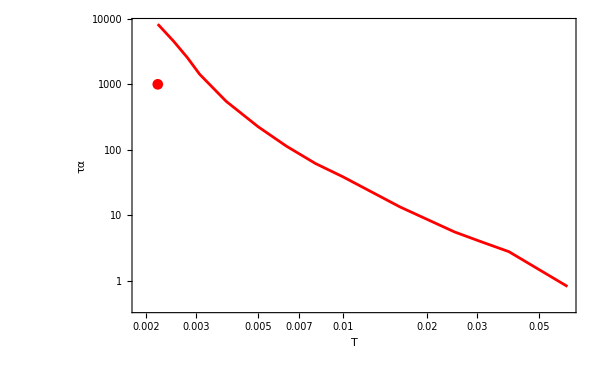

```mathematica
Show[ListLogLogPlot[Table[Table[{temperaturesOriginal[[s,T]],tauAlphasOriginal[[s,T]]},{T,Length[temperaturesOriginal[[s]]]}],{s,3,3}],FrameLabel->{"T","τα"},ImageSize->600,PlotRange->{All,All},Joined->True,PlotStyle->redBluePlotConfig[Length[p0sOriginal]]],ListLogLogPlot[Table[Table[{HelenT[[s,T]],HelentauAlpha[[s,T]]},{T,Length[HelenT[[s]]]}],{s,3,3}],FrameLabel->{"T","τα"},ImageSize->600,PlotRange->{All,All},Joined->False,PlotMarkers->Automatic,PlotStyle->redBluePlotConfig[Length[p0sOriginal]]]]
```

## fitting

```mathematica
p0s={3.75,3.815,3.80,3.825,3.85};
```

```mathematica
temperatures={{0.013,0.0115,0.0105,0.0096},{0.063,0.025,0.01,0.0063,0.005,0.00385,0.0028,0.0022,0.0015,0.0012,0.001,0.0008,0.00067},{0.002,0.0018,0.0016},{0.0022,0.0013,0.00033,0.00025,0.00018,0.00014,0.0001},{0.00067,0.00018}};
```

```mathematica
records={{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10,11,12,13,14,15,16,17,18,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19}};
```

```mathematica
tauEstimate={{1000,1000,3000,10000},{1000,1000,1000,1000,1000,1000,1000,3000,5000,10000,10000,10000, 10000},{10000,10000,10000},{1000,1000,10000,10000,10000,10000,10000},{1000,3000}};
```

```mathematica
CRSISF=Table[Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p","/timeCRSISF_N4096_p","_T","_k6.800_waitingTime","_idx",".nc"},{p0s[[p]],p0s[[p]],temperatures[[p,T]],Floor[If[tauEstimate[[p,T]]==999999,tauEstimate[[p,T]],If[tauEstimate[[p,T]]<1000,10000,tauEstimate[[p,T]]*10]]
],records[[p,i]]},{3,4,8,0,0}],"Data"],{i,Length[records[[p]]]}],$Failed],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.815/timeCRSISF_N4096_p3.8150_T0.06300000_k6.800_waitingTime10000_idx16.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.815/timeCRSISF_N4096_p3.8150_T0.06300000_k6.800_waitingTime10000_idx17.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.815/timeCRSISF_N4096_p3.8150_T0.02500000_k6.800_waitingTime10000_idx15.nc not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Import::format: Cannot import data as Data.

General::stop: Further output of Import::format will be suppressed during this calculation.

```mathematica
CRSISF[[1,1,1,1,1]]
```

10000.

```mathematica
meanCRFAll=Table[Table[Table[{CRSISF[[p,T,1,1,rec]]-CRSISF[[p,T,1,1,1]],Mean[Table[CRSISF[[p,T,i,2,rec]],{i,Length[CRSISF[[p,T]]]}]]},{rec,Min[Table[Length[CRSISF[[p,T,i,1]]],{i,Length[CRSISF[[p,T]]]}]]}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

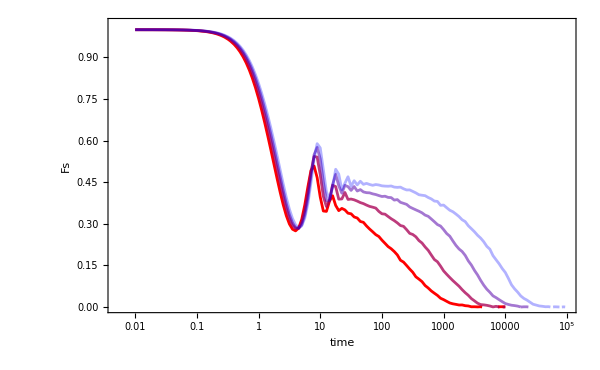
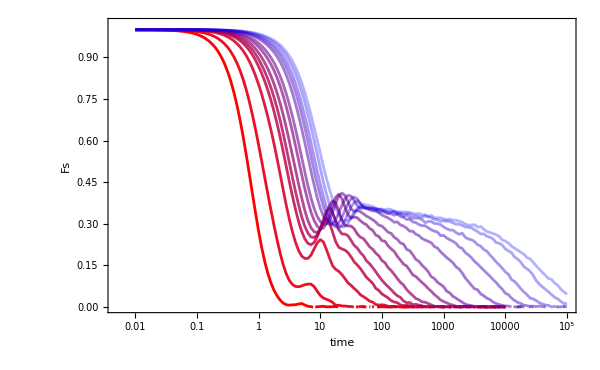
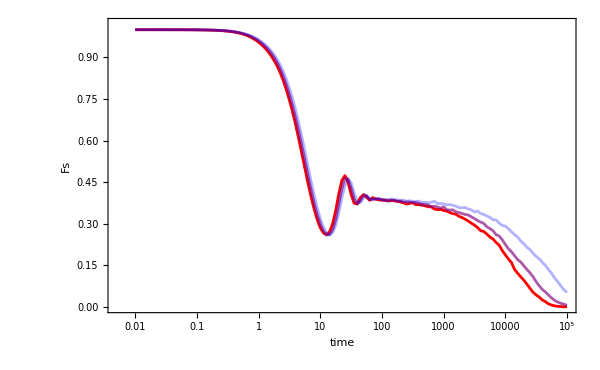
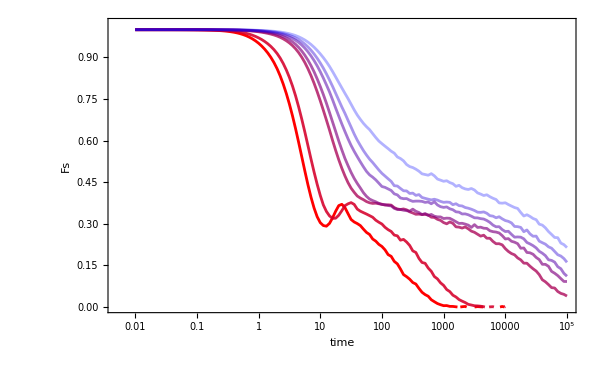
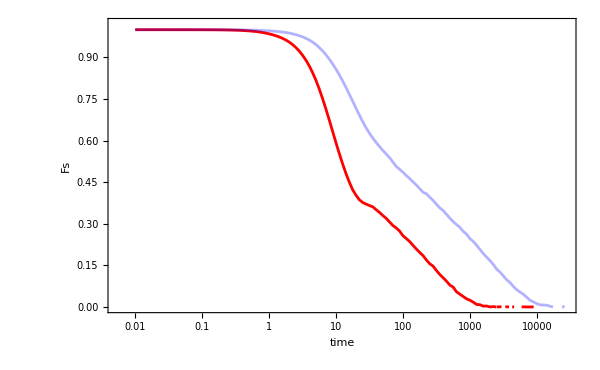

```mathematica
Table[Show[ListLogLinearPlot[Table[meanCRFAll[[p,T]],{T,Length[temperatures[[p]]]}],PlotRange->{All,{0,1.02}},PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],ImageSize->600,Joined->True,FrameLabel->{"time","Fs"}]],{p,Length[p0s]}]
```

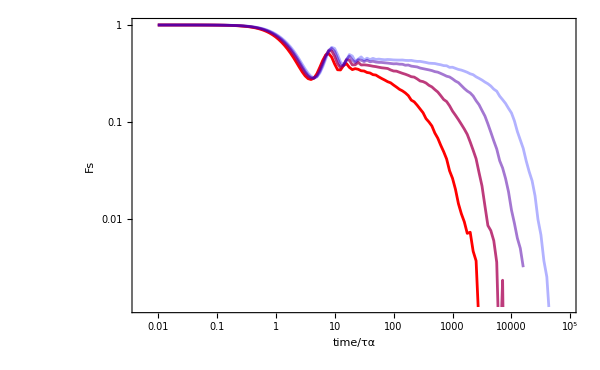
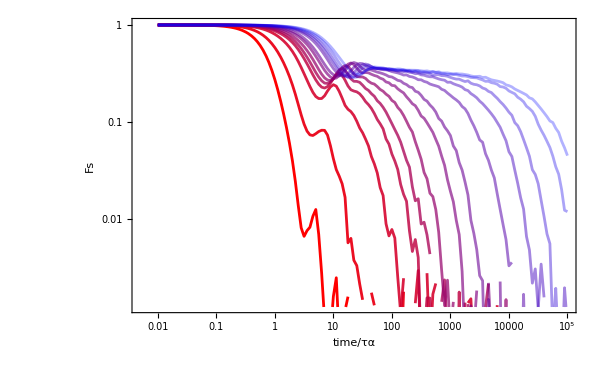
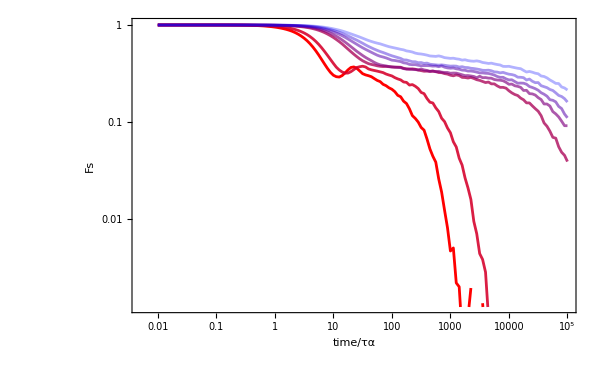
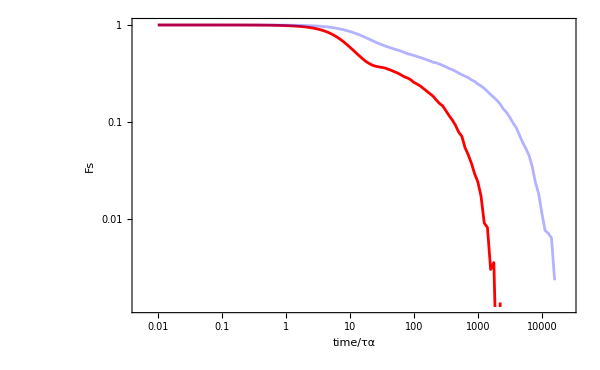

```mathematica
Table[Show[ListLogLogPlot[Table[meanCRFAll[[p,T]],{T,Length[temperatures[[p]]]}],PlotRange->{All,{0,1.02}},PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],ImageSize->600,Joined->True,FrameLabel->{"time/τα","Fs"}]],{p,Length[p0s]}]
```

### fitting

```mathematica
stretchedExp[t_,G_,τ_,β_]:=G Exp[-(t/τ)^β];
```

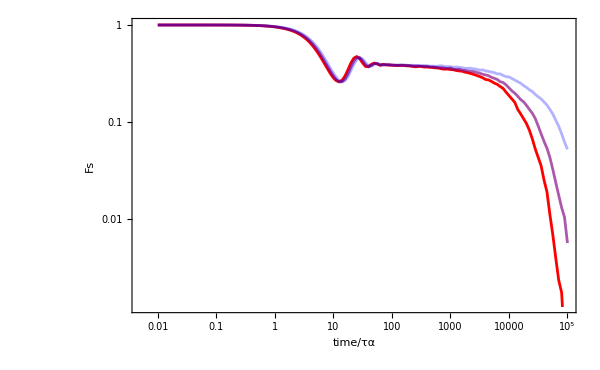

```mathematica
Table[Show[ListLogLogPlot[Table[meanCRFAll[[p,T]],{T,Length[temperatures[[p]]]}],PlotRange->{All,{0,1.02}},PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],ImageSize->600,Joined->True,FrameLabel->{"time/τα","Fs"}]],{p,3,3}]
```

```mathematica
fitCRSISFStartNum={{56,100,100,150},{5,10,25,30,40,50,110,120,140,150,1000,1000,3000},{1500,1500,1500},{63,70,200,200,1600,1600,3000},{150,1000}};
```

```mathematica
fitStart=Table[Table[Position[Normal[meanCRFAll[[p,T,;;,1]]],_?(#>fitCRSISFStartNum[[p,T]]&)][[1,1]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{66,71,72,75},{45,51,59,61,64,65,72,73,74,75,92,92,101},{95,95,95},{67,68,78,78,96,96,101},{75,92}}

```mathematica
betaCons={0.9>β>0.3,0.82>β>0.3,0.85>β>0.3,0.9>β>0.3,0.9>β>0.3};
gCons={0.7>G>0.1};
```

```mathematica
meanfit=Table[Table[NonlinearModelFit[meanCRFAll[[p,T,fitStart[[p,T]];;]],{stretchedExp[t,G,τ,β],{betaCons[[p]],gCons[[1]],τ>0.5}},{G,τ,β},t],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…]}}

```mathematica
tauAlphas=Table[Table[meanfit[[p,T]]["BestFitParameters"][[2,2]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{243.711,913.227,2655.03,7197.08},{0.874672,3.49786,17.3897,39.1317,63.35,120.739,257.705,505.731,1796.19,4541.59,10039.4,24964.3,39852.3},{13357.6,20354.1,44857.4},{200.671,567.113,27156.5,57750.2,76749.8,123179.,158055.},{318.229,2304.61}}

```mathematica
betas=Table[Table[meanfit[[p,T]]["BestFitParameters"][[3,2]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{0.709065,0.825344,0.899962,0.878365},{0.816036,0.812522,0.81567,0.815299,0.81824,0.81983,0.77786,0.797223,0.819914,0.800987,0.819974,0.819968,0.729751},{0.849983,0.849963,0.810242},{0.840445,0.83583,0.5867,0.574956,0.578717,0.556846,0.545565},{0.889535,0.816369}}

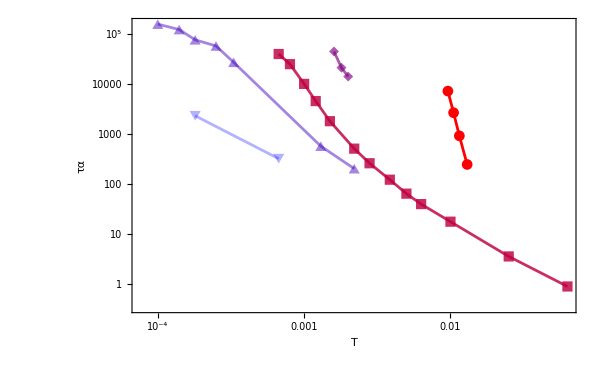

```mathematica
Show[ListLogLogPlot[Table[Table[{temperatures[[s,T]],tauAlphas[[s,T]]},{T,Length[temperatures[[s]]]}],{s,Length[p0s]}],FrameLabel->{"T","τα"},ImageSize->600,PlotRange->{All,All},Joined->True,PlotMarkers->Automatic,PlotStyle->redBluePlotConfig[Length[p0s]]]]
```

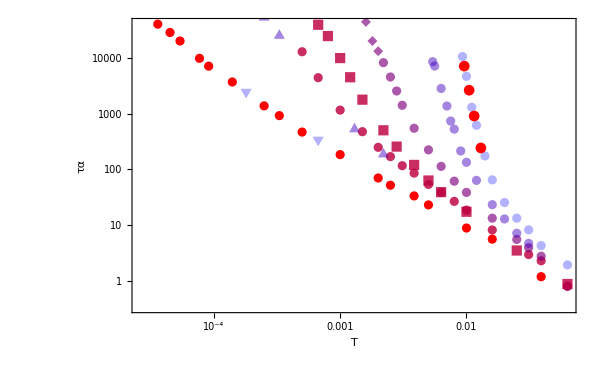

```mathematica
Show[ListLogLogPlot[Table[Table[{temperaturesOriginal[[s,T]],tauAlphasOriginal[[s,T]]},{T,Length[temperaturesOriginal[[s]]]}],{s,Length[p0sOriginal]}],FrameLabel->{"T","τα"},ImageSize->600,PlotRange->{All,All},Joined->False,PlotStyle->redBluePlotConfig[Length[p0sOriginal]]],ListLogLogPlot[Table[Table[{temperatures[[s,T]],tauAlphas[[s,T]]},{T,Length[temperatures[[s]]]}],{s,Length[p0s]}],FrameLabel->{"T","τα"},ImageSize->600,PlotRange->{All,All},Joined->False,PlotMarkers->Automatic,PlotStyle->redBluePlotConfig[Length[p0s]]]]
```

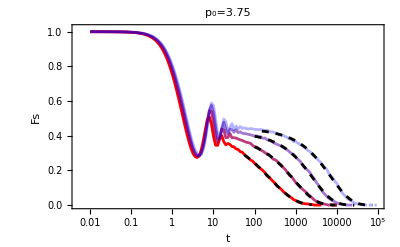
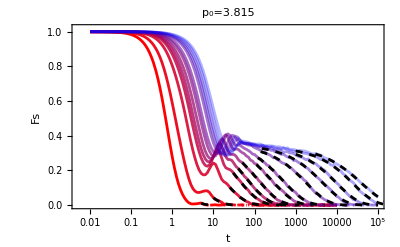
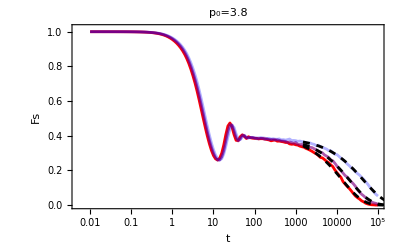
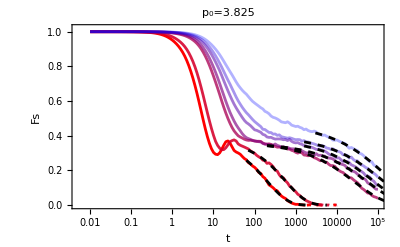
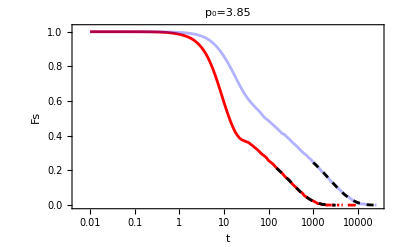

```mathematica
fsPlots=Table[Show[ListLogLinearPlot[Table[meanCRFAll[[p,T]],{T,Length[temperatures[[p]]]}],PlotRange->{All,{0,1.02}},PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],ImageSize->400,Joined->True,PlotLabel->"p_0="<>ToString[p0s[[p]]],FrameLabel->{"t","Fs"}],Table[LogLinearPlot[meanfit[[p,T]][x],{x,fitCRSISFStartNum[[p,T]],meanfit[[p,T]]["BestFitParameters"][[2,2]]*10},PlotStyle->{Black,Dashed}],{T,Length[temperatures[[p]]]}]],{p,Length[p0s]}]
```

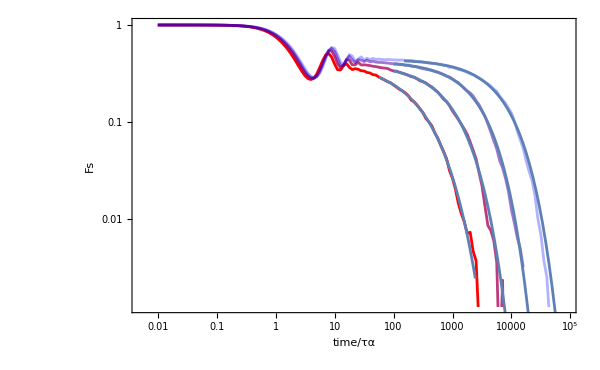
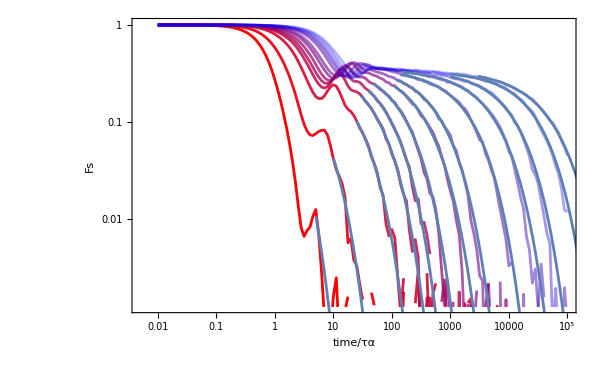
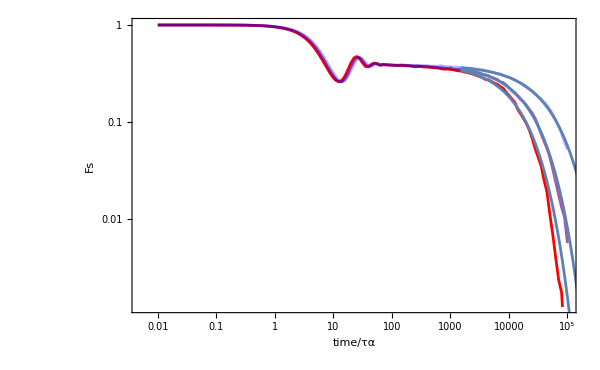
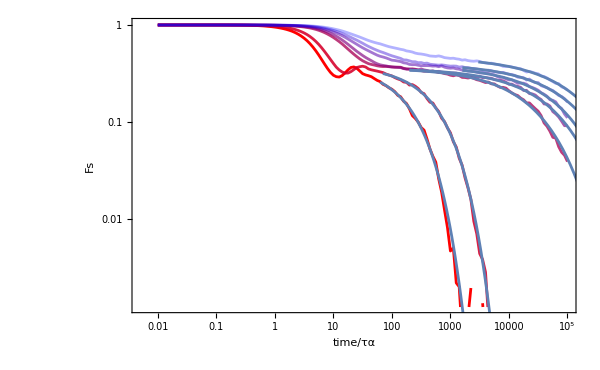
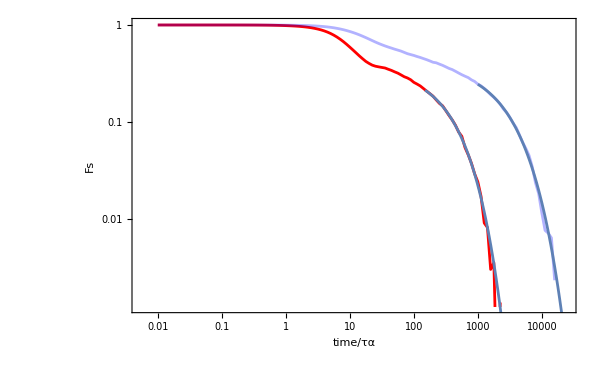

```mathematica
Table[Show[ListLogLogPlot[Table[meanCRFAll[[p,T]],{T,Length[temperatures[[p]]]}],PlotRange->{All,{0,1.02}},PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],ImageSize->600,Joined->True,FrameLabel->{"time/τα","Fs"}],Table[LogLogPlot[meanfit[[p,T]][x],{x,fitCRSISFStartNum[[p,T]],meanfit[[p,T]]["BestFitParameters"][[2,2]]*10}],{T,Length[temperatures[[p]]]}]],{p,Length[p0s]}]
```

```mathematica
outputTable=Flatten[Table[Table[{p0s[[p]],temperatures[[p,T]],tauAlphas[[p,T]]},{T,Length[temperatures[[p]]]}],{p,{1,3,2,4,5}}],1]
```

{{3.75,0.013,243.711},{3.75,0.0115,913.227},{3.75,0.0105,2655.03},{3.75,0.0096,7197.08},{3.8,0.002,13357.6},{3.8,0.0018,20354.1},{3.8,0.0016,44857.4},{3.815,0.063,0.874672},{3.815,0.025,3.49786},{3.815,0.01,17.3897},{3.815,0.0063,39.1317},{3.815,0.005,63.35},{3.815,0.00385,120.739},{3.815,0.0028,257.705},{3.815,0.0022,505.731},{3.815,0.0015,1796.19},{3.815,0.0012,4541.59},{3.815,0.001,10039.4},{3.815,0.0008,24964.3},{3.815,0.00067,39852.3},{3.825,0.0022,200.671},{3.825,0.0013,567.113},{3.825,0.00033,27156.5},{3.825,0.00025,57750.2},{3.825,0.00018,76749.8},{3.825,0.00014,123179.},{3.825,0.0001,158055.},{3.85,0.00067,318.229},{3.85,0.00018,2304.61}}

```mathematica
Export["/home/chengling/Research/updates/2026_04_21/additionalTauAlpha.csv",Prepend[outputTable,{"p","T","tauAlpha"}]]
```

/home/chengling/Research/updates/2026_04_21/additionalTauAlpha.csv

```mathematica
Export["/home/chengling/Research/updates/2026_04_06/fsPlots.jpeg",fsPlots,ImageResolution->300]
```

/home/chengling/Research/updates/2026_04_06/fsPlots.jpeg

## fitting 2026_06_06

```mathematica
p0s={3.75,3.815,3.80,3.825,3.85};
```

```mathematica
temperatures={{0.013,0.0115,0.0105,0.0096},{0.063,0.025,0.01,0.0063,0.005,0.00385,0.0028,0.0022,0.0015,0.0012,0.001,0.0008,0.00067},{0.002,0.0018,0.0016},{0.0022,0.0013,0.00033,0.00025,0.00018,0.00014,0.0001},{0.00067,0.00018}};
```

```mathematica
records={{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10,11,12,13,14,15,16,17,18,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19}};
```

```mathematica
tauEstimate={{1000,1000,3000,10000},{1000,1000,1000,1000,1000,1000,1000,3000,5000,10000,10000,10000, 10000},{10000,10000,10000},{1000,1000,10000,10000,10000,10000,10000},{1000,3000}};
```

```mathematica
CRSISF=Table[Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p","/timeCRSISF_N4096_p","_T","_k6.800_waitingTime","_idx",".nc"},{p0s[[p]],p0s[[p]],temperatures[[p,T]],Floor[If[tauEstimate[[p,T]]==999999,tauEstimate[[p,T]],If[tauEstimate[[p,T]]<1000,10000,tauEstimate[[p,T]]*10]]
],records[[p,i]]},{3,4,8,0,0}],"Data"],{i,Length[records[[p]]]}],$Failed],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.815/timeCRSISF_N4096_p3.8150_T0.06300000_k6.800_waitingTime10000_idx16.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.815/timeCRSISF_N4096_p3.8150_T0.06300000_k6.800_waitingTime10000_idx17.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.815/timeCRSISF_N4096_p3.8150_T0.02500000_k6.800_waitingTime10000_idx15.nc not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

```mathematica
CRSISF[[1,1,1,1,1]]
```

10000.

```mathematica
meanCRFAll=Table[Table[Table[{CRSISF[[p,T,1,1,rec]]-CRSISF[[p,T,1,1,1]],Mean[Table[CRSISF[[p,T,i,2,rec]],{i,Length[CRSISF[[p,T]]]}]]},{rec,Min[Table[Length[CRSISF[[p,T,i,1]]],{i,Length[CRSISF[[p,T]]]}]]}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

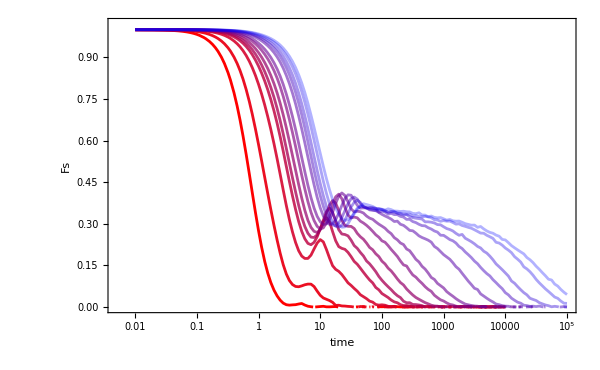
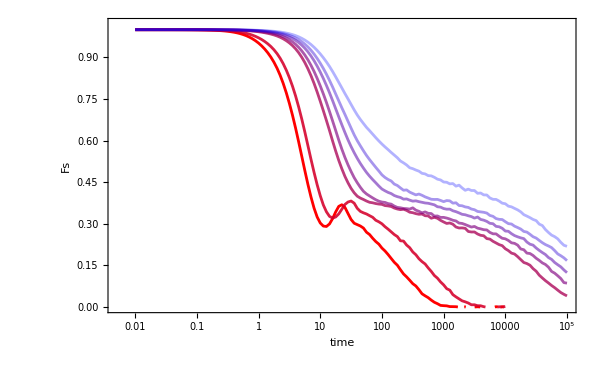
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Show[ListLogLinearPlot[Table[meanCRFAll[[p,T]],{T,Length[temperatures[[p]]]}],PlotRange->{All,{0,1.02}},PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],ImageSize->600,Joined->True,FrameLabel->{"time","Fs"}]],{p,Length[p0s]}]
```

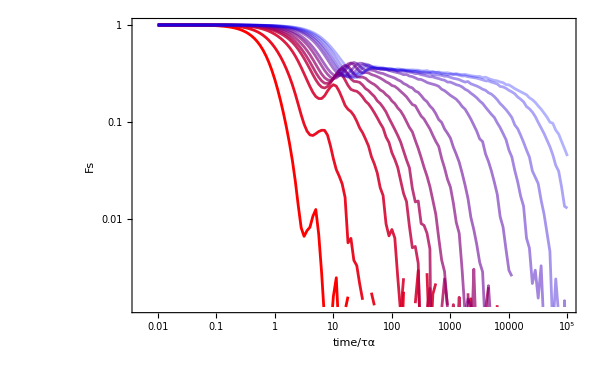
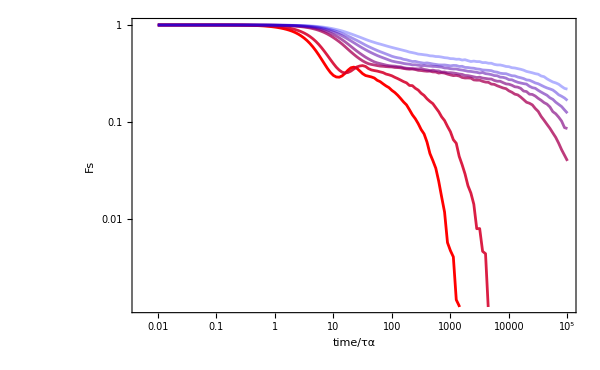
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Show[ListLogLogPlot[Table[meanCRFAll[[p,T]],{T,Length[temperatures[[p]]]}],PlotRange->{All,{0,1.02}},PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],ImageSize->600,Joined->True,FrameLabel->{"time/τα","Fs"}]],{p,Length[p0s]}]
```

### fitting

```mathematica
stretchedExp[t_,G_,τ_,β_]:=G Exp[-(t/τ)^β];
```

```mathematica
Table[Show[ListLogLogPlot[Table[meanCRFAll[[p,T]],{T,Length[temperatures[[p]]]}],PlotRange->{All,{0,1.02}},PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],ImageSize->600,Joined->True,FrameLabel->{"time/τα","Fs"}]],{p,3,3}]
```

{-Graphics-}

```mathematica
fitCRSISFStartNum={{56,100,100,150},{5,10,25,30,40,50,110,120,140,150,1000,1000,3000},{1500,1500,1500},{63,70,200,200,1600,1600,3000},{150,1000}};
```

```mathematica
fitStart=Table[Table[Position[Normal[meanCRFAll[[p,T,;;,1]]],_?(#>fitCRSISFStartNum[[p,T]]&)][[1,1]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{66,71,72,75},{45,51,59,61,64,65,72,73,74,75,92,92,101},{95,95,95},{67,68,78,78,96,96,101},{75,92}}

```mathematica
betaCons={0.9>β>0.3,0.82>β>0.3,0.85>β>0.3,0.9>β>0.3,0.9>β>0.3};
gCons={0.7>G>0.1};
```

```mathematica
meanfit=Table[Table[NonlinearModelFit[meanCRFAll[[p,T,fitStart[[p,T]];;]],{stretchedExp[t,G,τ,β],{betaCons[[p]],gCons[[1]],τ>0.5}},{G,τ,β},t],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…]}}

```mathematica
meanfit[[-2]]=Flatten[Table[Table[NonlinearModelFit[meanCRFAll[[p,T,fitStart[[p,T]];;]],{stretchedExp[t,G,τ,β],{{0.9>β>0.3,0.9>β>0.83,0.9>β>0.3,0.7>β>0.55,0.7>β>0.55,0.9>β>0.55,0.9>β>0.55}[[T]],gCons[[1]],τ>0.5}},{G,τ,β},t],{T,Length[temperatures[[p]]]}],{p,-2,-2}]]
```

```mathematica
tauAlphas=Table[Table[meanfit[[p,T]]["BestFitParameters"][[2,2]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{243.711,913.227,2655.03,7197.08},{0.874672,3.49786,17.3897,40.5313,63.1859,123.006,245.245,473.63,1783.43,4554.69,9590.44,25243.9,39867.7},{13357.6,20354.1,44857.4},{191.139,527.294,27763.3,52515.7,83145.2,122940.,156387.},{318.229,2304.61}}

```mathematica
tauAlphasOLD={{243.71095843994792,913.2265518556721,2655.025680274773,7197.07876080598},{0.8746718197576249,3.497855621381444,17.389663907294754,39.13172538294689,63.34999300440773,120.73942671437906,257.70484274906863,505.7313045249323,1796.1888100614794,4541.593418928466,10039.366326794478,24964.276925687253,39852.28971885045},{13357.577764299964,20354.12033883563,44857.43365079655},{200.67097888793637,567.113302803893,27156.49508963715,57750.21947695971,76749.80459933728,123179.39601936424,158054.96542269463},{318.2288353798615,2304.6134408695957}};
```

```mathematica
betas=Table[Table[meanfit[[p,T]]["BestFitParameters"][[3,2]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{0.709065,0.825344,0.899962,0.878365},{0.816036,0.812522,0.81567,0.818844,0.818534,0.819619,0.763167,0.782079,0.819927,0.803389,0.819961,0.819967,0.754139},{0.849983,0.849963,0.810242},{0.843438,0.761103,0.570122,0.510148,0.54621,0.468895,0.501937},{0.889535,0.816369}}

```mathematica
betasOLD={{0.7090650422130831,0.8253435204899078,0.8999617085029218,0.8783645979548735},{0.8160362133401304,0.8125216236688994,0.8156704275370408,0.8152988412412486,0.8182402690070313,0.8198302983052117,0.7778603501355402,0.7972229110872096,0.8199139378085745,0.8009870870515726,0.819973997853334,0.8199676430450565,0.7297506407266817},{0.8499830040980654,0.849963137862561,0.8102424021874369},{0.8404451188382167,0.8358304778154356,0.5866999370221897,0.5749564707313377,0.5787171978454863,0.5568456765737532,0.5455648693924222},{0.8895350282748089,0.8163686653780313}};
```

```mathematica
meanfit[[-2]]=Flatten[Table[Table[NonlinearModelFit[meanCRFAll[[p,T,fitStart[[p,T]];;]],{stretchedExp[t,G,τ,β],{{0.9>β>0.3,0.9>β>0.83,0.9>β>0.3,0.7>β>0.55,0.7>β>0.55,0.9>β>0.55,0.9>β>0.55}[[T]],gCons[[1]],τ>0.5}},{G,τ,β},t],{T,Length[temperatures[[p]]]}],{p,-2,-2}]]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
tauAlphas=Table[Table[meanfit[[p,T]]["BestFitParameters"][[2,2]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{243.711,913.227,2655.03,7197.08},{0.874672,3.49786,17.3897,40.5313,63.1859,123.006,245.245,473.63,1783.43,4554.69,9590.44,25243.9,39867.7},{13357.6,20354.1,44857.4},{191.139,570.906,27763.3,53312.4,83359.9,124726.,156441.},{318.229,2304.61}}

```mathematica
betas=Table[Table[meanfit[[p,T]]["BestFitParameters"][[3,2]],{T,Length[temperatures[[p]]]}],{p,-2,-2}]
```

{{0.843438,0.83004,0.570122,0.55002,0.550669,0.55004,0.550096}}

```mathematica
betasOLD[[-2]]
```

{0.840445,0.83583,0.5867,0.574956,0.578717,0.556846,0.545565}

```mathematica
Table[Table[tauAlphas[[p,T]]/tauAlphasOLD[[p,T]]-1,{T,Length[temperatures[[p]]]}],{p,-2,-2}]
```

{{-0.0475012,0.00668748,0.0223459,-0.0768455,0.0861246,0.012552,-0.0102093}}

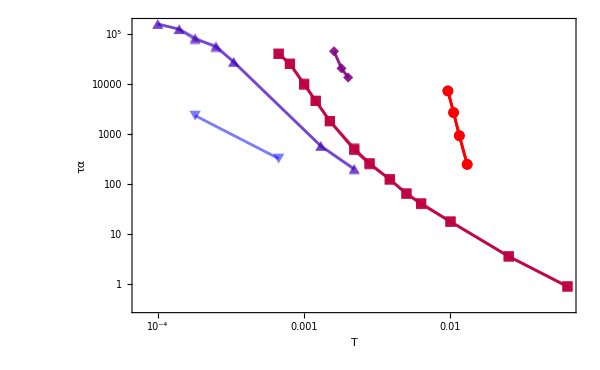

```mathematica
Show[ListLogLogPlot[Table[Table[{temperatures[[s,T]],tauAlphas[[s,T]]},{T,Length[temperatures[[s]]]}],{s,Length[p0s]}],FrameLabel->{"T","τα"},ImageSize->600,PlotRange->{All,All},Joined->True,PlotMarkers->Automatic,PlotStyle->redBluePlotConfig[Length[p0s]]],ListLogLogPlot[Table[Table[{temperatures[[s,T]],tauAlphasOLD[[s,T]]},{T,Length[temperatures[[s]]]}],{s,Length[p0s]}],FrameLabel->{"T","τα"},ImageSize->600,PlotRange->{All,All},Joined->True,PlotMarkers->Automatic,PlotStyle->redBluePlotConfig[Length[p0s]]]]
```

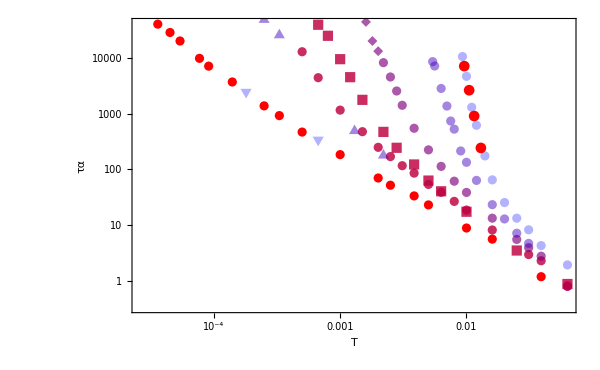

```mathematica
Show[ListLogLogPlot[Table[Table[{temperaturesOriginal[[s,T]],tauAlphasOriginal[[s,T]]},{T,Length[temperaturesOriginal[[s]]]}],{s,Length[p0sOriginal]}],FrameLabel->{"T","τα"},ImageSize->600,PlotRange->{All,All},Joined->False,PlotStyle->redBluePlotConfig[Length[p0sOriginal]]],ListLogLogPlot[Table[Table[{temperatures[[s,T]],tauAlphas[[s,T]]},{T,Length[temperatures[[s]]]}],{s,Length[p0s]}],FrameLabel->{"T","τα"},ImageSize->600,PlotRange->{All,All},Joined->False,PlotMarkers->Automatic,PlotStyle->redBluePlotConfig[Length[p0s]]]]
```

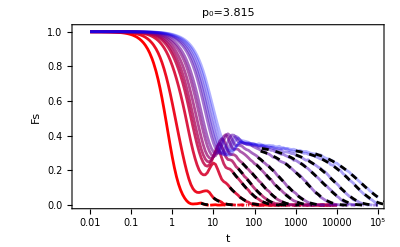
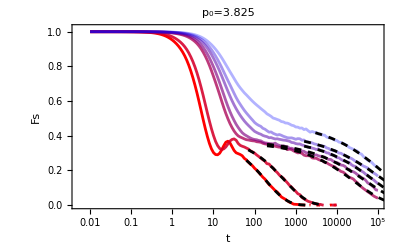
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
fsPlots=Table[Show[ListLogLinearPlot[Table[meanCRFAll[[p,T]],{T,Length[temperatures[[p]]]}],PlotRange->{All,{0,1.02}},PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],ImageSize->400,Joined->True,PlotLabel->"p_0="<>ToString[p0s[[p]]],FrameLabel->{"t","Fs"}],Table[LogLinearPlot[meanfit[[p,T]][x],{x,fitCRSISFStartNum[[p,T]],meanfit[[p,T]]["BestFitParameters"][[2,2]]*10},PlotStyle->{Black,Dashed}],{T,Length[temperatures[[p]]]}]],{p,Length[p0s]}]
```

```mathematica
Table[Show[ListLogLogPlot[Table[meanCRFAll[[p,T]],{T,Length[temperatures[[p]]]}],PlotRange->{All,{0,1.02}},PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],ImageSize->600,Joined->True,FrameLabel->{"time/τα","Fs"}],Table[LogLogPlot[meanfit[[p,T]][x],{x,fitCRSISFStartNum[[p,T]],meanfit[[p,T]]["BestFitParameters"][[2,2]]*10}],{T,Length[temperatures[[p]]]}]],{p,Length[p0s]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
outputTable=Flatten[Table[Table[{p0s[[p]],temperatures[[p,T]],tauAlphas[[p,T]]},{T,Length[temperatures[[p]]]}],{p,{1,3,2,4,5}}],1]
```

{{3.75,0.013,243.711},{3.75,0.0115,913.227},{3.75,0.0105,2655.03},{3.75,0.0096,7197.08},{3.8,0.002,13357.6},{3.8,0.0018,20354.1},{3.8,0.0016,44857.4},{3.815,0.063,0.874672},{3.815,0.025,3.49786},{3.815,0.01,17.3897},{3.815,0.0063,40.5313},{3.815,0.005,63.1859},{3.815,0.00385,123.006},{3.815,0.0028,245.245},{3.815,0.0022,473.63},{3.815,0.0015,1783.43},{3.815,0.0012,4554.69},{3.815,0.001,9590.44},{3.815,0.0008,25243.9},{3.815,0.00067,39867.7},{3.825,0.0022,191.139},{3.825,0.0013,527.294},{3.825,0.00033,27763.3},{3.825,0.00025,52515.7},{3.825,0.00018,83145.2},{3.825,0.00014,122940.},{3.825,0.0001,156387.},{3.85,0.00067,318.229},{3.85,0.00018,2304.61}}

```mathematica
Export["/home/chengling/Research/updates/2026_06_06/additionalTauAlpha_2026_06_06.csv",Prepend[outputTable,{"p","T","tauAlpha"}]]
```

/home/chengling/Research/updates/2026_06_06/additionalTauAlpha_2026_06_06.csv

```mathematica
Export["/home/chengling/Research/updates/2026_06_06/fsPlots.jpeg",fsPlots,ImageResolution->300]
```

/home/chengling/Research/updates/2026_06_06/fsPlots.jpeg

```mathematica
Table[Table[tauAlphas[[p,T]]/tauAlphasOLD[[p,T]]-1,{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{0.,0.,0.,0.},{0.,0.,0.,0.0357647,-0.00258996,0.0187696,-0.0483482,-0.0634741,-0.00710383,0.00288265,-0.0447169,0.011202,0.000385821},{0.,0.,0.},{-0.0475012,0.00668748,0.0223459,-0.0768455,0.0861246,0.012552,-0.0102093},{-1.11022×10^-16,0.}}

```mathematica
tauAlphas[[-2]]
```

{191.139,527.294,27763.3,52515.7,83145.2,122940.,156387.}

```mathematica
tauAlphasOLD[[-2]]
```

{200.671,567.113,27156.5,57750.2,76749.8,123179.,158055.}